```mathematica
<<Matcher`;
<<Classifier`;
```

```mathematica
?VF
```

VF[true_group, predicted_group] returns Error rate, FAR and FRR

```mathematica
(*use Distance_cls_nxr.nb here*)
```

```mathematica
pg=classifyDist1[sdata,templ,1.3];
```

```mathematica
rr=Reap[For[i=0,i<4,i=i+0.05,
Sow[VF[tg,classifyDist1[sdata,templ,i]][[{2,3}]]];
]][[2,1]];
```

```mathematica
ListPlot[rr*100,Joined->True,Frame->True,FrameLabel->{"FAR (%)","FRR (%)"},AxesOrigin->{0,0},PlotStyle->Dashed]
```

```mathematica
(*EER*)
```

```mathematica
For[i=7,i<8,i=i+0.002,
{far,frr}=VF[tg,classifyDist1[pdata,templ,i]][[{2,3}]];
If[Abs[far-frr]≤0.005,Break[]];
];
{i,far,frr}
```

{7.534,0.161633,0.16}

```mathematica
VF[tg,classifyDist1[pdata,templ,7.5336]]
```

{0.1612,0.161224,0.16}

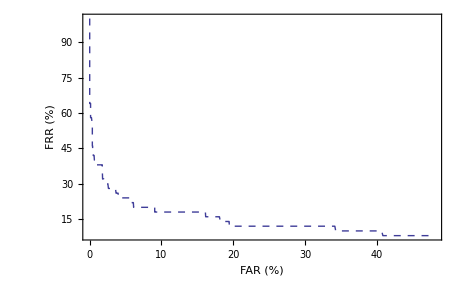

```mathematica
pg=RocPlot[pdata,templ,tg,classifyDist1]
```